```mathematica
Remove["Global`*"]
expη[x_, η_] := If[η==1, Exp[x],(1+(1-η) x)^(1/(1-η))];
logη[x_, η_] :=If[η==1, Log[x], 1/(1-η)(x^(1-η)-1)];
```

```mathematica
SetOptions[{Plot,LogLogPlot,ListLogPlot, ListPlot, ListLogLogPlot, ListLogLinearPlot},
Frame-> True,
LabelStyle->{FontFamily->"Arial", FontSize->12},
AspectRatio->1];
SetOptions[{ListLogPlot, ListLogLinearPlot},  Joined->True, FrameLabel->{"x", " "}];
```

#### Plot to show the characteristic scale in expη(x)

```mathematica
F1[ηVal_]:=Module[{pos, xMax, xMin, yMin, yMax, xStar, η, p1, p2, p3, p4},
pos=0.9;
xMax = 100;
xMin = 0.1;
yMin = 10^-10;
yMax = 10^15;
xStar = 1/(1 - ηVal);
p1 = LogLogPlot[Exp[x],{x,xMin,xMax},PlotStyle->{Blue,PointSize[.02]},PlotRange->{yMin, yMax},   PlotLegends->Placed[{"e^x"}, {0.26, pos}]];
p2= LogLogPlot[expη[x, ηVal],{x,xMin,xMax},PlotStyle->{Gray,PointSize[.02]},PlotRange->All,   PlotLegends->Placed[{"exp_η(x)"}, {0.26, pos-0.15}]];
p3 = LogLogPlot[((1-η)x)^(1/(1-η)) /. η-> ηVal,{x,xMin,xMax},PlotStyle->{Red,PointSize[.02]},PlotRange->All,   PlotLegends->Placed[{"((1-η) x)^(1/(1 - η))"}, {0.26, pos-0.3}]];
p4 = ParametricPlot[{Log@xStar,Log@u},{u,yMin,yMax},PlotStyle->{Black, Dashed}];
txt=Graphics[Text[Style["x_*", 12],{Log @ (0.75xStar),Log @ (10yMin)}]];
Show[{p1,p2, p3, p4, txt},
FrameLabel->{"x", "exp_η(x)"}]
]
```

#### Plot to show the smoothness of expη

```mathematica
F2[η_]:=Module[{pos, xMax, xMin, yMin, yMax, p1, p2, p3},
xMax = 100;
xMin = 0.1;
yMin = 1/10;
yMax = 10^10;
pos=0.9;
p1 = LogLogPlot[Exp[x],{x,xMin,xMax},PlotStyle->{Blue,PointSize[.02]},PlotRange->{yMin, yMax},   PlotLegends->Placed[{"e^x"}, {0.26, pos}]];
p2= LogLogPlot[expη[x, η],{x,xMin,xMax},PlotStyle->{Gray,PointSize[.02]},PlotRange->All,   PlotLegends->Placed[{"exp_η(x) η = "<>ToString[η]}, {0.26, pos-0.15}]];
p3 = LogLogPlot[1+x,{x,xMin,xMax},PlotStyle->{Red,PointSize[.02]},PlotRange->All,   PlotLegends->Placed[{"1+x"}, {0.26, pos-0.3}]];
Show[{p1,p2, p3},
FrameLabel->{"x", "exp_η(x)"}]
]
```

#### Plot to show the η-compounding random walk

```mathematica
step[x_, b_, z1_, z2_, η_] :=If[b ==0, expη[logη[x, η]+ logη[z1,η], η], expη[logη[x,η]+ logη[z2,η], η]];
F3[B_,η_]:=Module[{X0, T, M, z1, z2, X, i, j,c,linestyles, sampleTrajectories},
X0 = 1; T =Dimensions[B][[1]]; M = Dimensions[B][[2]]; z1 = 15/8; z2 = 9/8;
linestyles = Table[{GrayLevel[RandomReal[]], Thickness[0.002]}, {i,1,M}];
X = Table[0,{i,1,T+1}, {j,1,M}];
For[j=1, j<= M, j++, 
X[[1,j]]= X0;
For[i=2, i<= T+1, i++,
c = B[[i-1,j]];
X[[i,j]]= N[step[X[[i-1, j]], c, z1, z2, η]];
];
];
sampleTrajectories=TemporalData[X[[1;;T+1, 1;;M]],{Table[i-1, {i,1, T+1}]}];
p1 = ListLogLogPlot[sampleTrajectories,PlotStyle->linestyles,PlotRange->{{1,T},{1/10,10^10}}, Joined->True,  PlotLegends->Placed[{"Sample paths η = "<>ToString[η]}, {0.26, 0.90}]];
Show[p1, FrameLabel->{"T", "X_T"}]

]
```

#### Plot to show the Laplace method

```mathematica
ϕ[x_, p_, q_, z1_, z2_ ] :=x Log[p] + (1-x)Log[q] +x Log[z1] + (1-x)Log[z2] -x Log[x] - (1-x)Log[1-x];
F[x_] := 1/(√(2 π x(1-x)));
F4[T_]:=Module[{X0, M, z1, z2,p,q, p1,pos},
X0 = 1; p=1/2;q=1/2; z1 = 15/8; z2 = 9/8; pos=0.9;
p1=Plot[F[x]/(√T) Exp[T ϕ[x,p,q,z1, z2] ], {x, 0, 1},PlotLegends->Placed[{"T = "<>ToString[T]}, {0.26, pos}]];
Show[p1,
FrameLabel->{"x", "I_0(x, T)"}]]
```

#### Plot to show the integrands in the Laplace method

```mathematica
F5[p_, z1_, z2_]:=Module[{q, pos, p1, p2, yMin, yMax,L},
pos = 0.9;
yMin = -1;
yMax = 1;
q=1-p; 
L ="p = "<>ToString[p]<> " z1 = "<>ToString[z1] <> " z2 =" <> ToString[z2];
p1=Plot[ϕ[x,p,q,z1, z2], {x, 0, 1}, PlotStyle->{Blue,PointSize[.02]},PlotRange->{yMin, yMax},PlotLegends->Placed[{"Multiplicative : η=1"}, {0.26, pos}], PlotLabel->L];
p2=Plot[ϕ[x,p,q,1, 1], {x, 0, 1}, PlotStyle->{Red,PointSize[.02]},PlotRange->{yMin, yMax},PlotLegends->Placed[{"Power : η<1"}, {0.20, pos-0.15}]];
Show[{p1,p2},
FrameLabel->{"x", "ϕ(x)"}]
]
```

#### Plot to show root as a function of the uniformity parameter, λ

```mathematica
F6[z1_,z2_, p_, q_, η_, X0_]:=Module[{ζ,L, A,x, p1, title},
ζ=1-η;
f[x_, λ_] := 2 ArcTanh[1- 2 x] + Log[p/q] + ((z1^ζ-z2^ζ)/(ζ X0^ζ+λ(x(z1^ζ-1)+(1-x)(z2^ζ-1))));
title ="p = "<>ToString[p]<> " z1 = "<>ToString[z1] <> " z2 =" <> ToString[z2] <> " η = " <> ToString[η];
L = Table[2^i,{i, Range[-10, 20, 1/2]}];
A= Table[{ λ, x /. FindRoot[f[x, λ], {x,9/10}]}, {λ, L}];
p1 = ListLogLinearPlot[A, FrameLabel->{"λ", "(x_λ^*)"}, PlotLabel->title, Joined->True];
p2 = LogLinearPlot[0.1325/(1+(x/10)^0.75) +0.6666, {x, 2^-10, 2^20}];
Show[p1, FrameLabel->{"λ", "x_λ^*"}]]
```

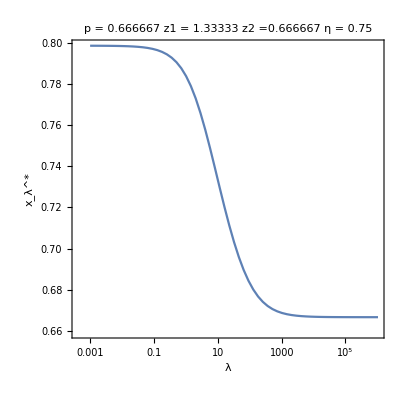

```mathematica
F6[4.0/3.0,2.0/3.0, 2.0/3.0, 1.0/3.0, 3.0/4.0, 1.0]
```

#### Plot of leading term in uniform asymptotic expansion

```mathematica
F7[z1_,z2_, p_, q_, η_, X0_, λ_]:=Module[{ζ,L, A,x, p1, title, φ, D2φ, t, Exmult, Exη, Exnum, F},
ζ=1-η;
φ[x_] := x Log[p] + (1-x)Log[q] -  x Log[x] -(1-x)Log[1-x] + 1/λ Log[(λ/ζ(x (z1^ζ-1) +(1-x)(z2^ζ-1)) + X0^ζ)];
D2φ[x_] := -(1/x+1/(1-x)+(λ(z1^ζ-z2^ζ)^2)/((ζ X0^ζ+ λ(x (z1^ζ-1) +(1-x)(z2^ζ-1)))^2));
F[x_] := 1/(√(2 π x (1-x)));
Exmult[t_] := X0 (p z1 + q z2)^t;
Exη[t_]:= (p (z1^ζ-1)+ q (z2^ζ-1) + X0^ζ/t)^(1/ζ)t^(1/ζ);
Exnum[t_, x_] := F[x] √((2π)/(- D2φ[x]))Exp[t φ[x]];
p1 = LogPlot[{Exnum[t,p], Exmult[t], Exη[t]}, {t,1, 200}, PlotLabels->{"Num", "Mult","η = "<>ToString[η]}];
Show[p1]
]
```

```mathematica
F7[4.0/3.0,2.0/3.0, 2.0/3.0, 1.0/3.0, 1./2., 1.0, 0.01]
```

-Graphics-

#### Smoothness of the limit η -> 1

```mathematica
Manipulate[F2[ηVal], {ηVal, 0.0, 1}]
```

#### Characteristic scale in expη(x)

```mathematica
Manipulate[F1[ηVal], {ηVal, 0.5, 1}]
```

#### Plot to show sample realisations of the η-compounding random walk

```mathematica
M=10; T= 150;
B = Table[RandomInteger[{0,1}],{i,1,T}, {j,1,M}];Manipulate[F3[B,ηVal], {ηVal, 0, 1}]
```

#### Plot to show continuum limit of the binomial distribution

```mathematica
Manipulate[F4[T], {T, 1, 100}]
```

#### Plot to show the exponents in the Laplace method

```mathematica
Manipulate[F5[p, z1,9.0/8.0], {p,0.1,0.9}, {z1,1,3}]
```

### Coefficients in the Stirling Series using Lagrange Inversion Theorem

```mathematica
f[t_] := √(2(Exp[t]-t-1))
```

```mathematica
Table[1/(n!)Limit[D[(t/f[t])^n, {t, n-1}], t->0, Direction->"FromAbove"] , {n,1,7}]
```

{1,-1/6,1/36,-1/270,1/4320,1/17010,-139/5443200}

```mathematica
Integrate[x^2 Exp[-t x^2/2], {x, -∞, ∞}, Assumptions->{t>0}]
```

(√(2 π))/t^(3/2)

```mathematica
rule = t -> τ - 1/6 τ^2 +1/36 τ^3-1/270 τ^4+ 1/4320 τ^5+1/17010 τ^6-139/5443200 τ^7
```

t→τ-τ^2/6+τ^3/36-τ^4/270+τ^5/4320+τ^6/17010-(139 τ^7)/5443200

#### Generate some figures

```mathematica
SetDirectory["/Users/colmconnaughton/LML/Projects/notes/gamma-compounding-note"];
```

```mathematica
p = F1[0.85];
Export["crossover.pdf",p]
p = F3[B,7/8];
Export["eta-random-walk.pdf",p]
```

crossover.pdf

eta-random-walk.pdf

```mathematica
p = F4[5.0];
Export["cont-limit-5.pdf",p]
p = F4[20.0];
Export["cont-limit-20.pdf",p]
```

cont-limit-5.pdf

cont-limit-20.pdf

```mathematica
p = F5[1.0/3.0, 2.4,9.0/8.0];
Export["laplace-method-phi.pdf",p]
```

laplace-method-phi.pdf

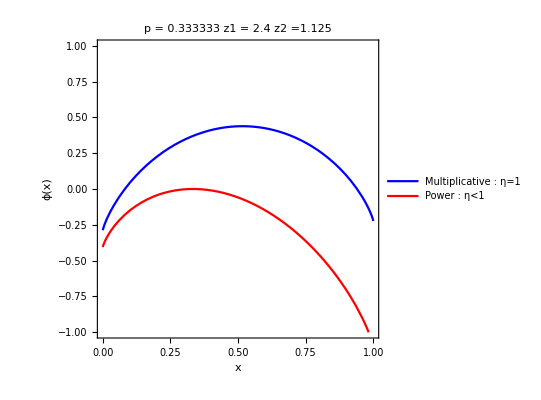

```mathematica
F5[1.0/3.0, 2.4,9.0/8.0]
```

```mathematica
p =F6[4.0/3.0,2.0/3.0, 2.0/3.0, 1.0/3.0, 3.0/4.0, 1.0];
Export["x_star_lambda.pdf",p]
```

x_star_lambda.pdf